```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/ETHUSD_BTCUSD_25SEP20/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

-Graphics-

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.88367,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.017498,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-06-17 01:00:00 | 234.03 | 9568.25 | -0.00558196 | -0.00484805
1 | 2020-06-17 02:00:00 | 232.7 | 9542.25 | -0.00569924 | -0.00272102
2 | 2020-06-17 03:00:00 | 232.46 | 9530.25 | -0.0010319 | -0.00125836
3 | 2020-06-17 04:00:00 | 232.85 | 9549.5 | 0.0016763 | 0.00201785
4 | 2020-06-17 05:00:00 | 233.09 | 9550.5 | 0.00103018 | 0.000104712
5 | 2020-06-17 06:00:00 | 232.6 | 9523.75 | -0.0021044 | -0.00280483
6 | 2020-06-17 07:00:00 | 234.3 | 9572.75 | 0.00728211 | 0.00513184
7 | 2020-06-17 08:00:00 | 234.7 | 9613.5 | 0.00170576 | 0.00424784
8 | 2020-06-17 09:00:00 | 233.99 | 9588.25 | -0.00302972 | -0.00262997)

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
tmp=Import[NotebookDirectory[] <> "data_eth_hourly/" <> ToString[kk] <> "_parameters.csv"]
```

(2020-06-17-01-00-00
1.04598
-0.123331
0.823254)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,5]]];
v=hatF[data[[2;;,6]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_eth_hourly/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.115838 | 0.0322194
0.0107998 | 0.0099398
0.51109 | 0.439931
0.586608 | 0.434391
0.9921 | 0.9903
0.865243 | 0.957901
0.971061 | 0.934361
0.713166 | 0.534309
0.583168 | 0.668947
0.98826 | 0.99346)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.085445,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{4.33884,1.92223,2.24936,2.16492,1.98759}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{3.77557,2.33934,2.11616,2.12167,1.89979}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.0366327,0.0636402,0.256639,0.654533,0.475287}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.0308757,0.0598254,0.253902,0.652118,0.473193}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

160.395

```mathematica
%/Length[data]
```

0.47595

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{17.704,191.299}

```mathematica
%/Length[data]
```

{0.0525341,0.567654}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=185, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,5]]];
v=hatF[data[[2;;,6]]];
tmp=Import[NotebookDirectory[] <> "data_eth_hourly/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

```mathematica
(*tLLnew={};
mLLnew={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
uv=Import[NotebookDirectory[] <> "data_xrp/" <> ToString[kk] <> "_simulation.csv"];
skd=SmoothKernelDistribution[uv];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLnew, ll];
AppendTo[mLLnew,mll];
]*)
```

```mathematica
tLL
```

{191.299,192.176,190.411,188.359,188.641,172.618,178.495,178.774,179.153,186.863,189.781,182.223,179.544,178.227,173.62,167.736,170.969,163.452,170.349,169.906,169.575,164.047,166.491,168.658,171.857,172.362,172.916,170.226,169.321,168.815,169.734,169.147,172.611,175.017,176.063,176.358,182.029,179.038,178.1,178.241,179.052,178.246,176.211,177.441,178.918,178.033,174.729,175.004,170.08,167.795,164.141,164.529,168.412,169.466,168.279,171.967,168.748,168.471,166.302,167.728,172.396,174.446,174.729,175.539,174.155,171.884,170.563,165.815,166.942,164.548,167.746,160.428,147.73,159.073,151.77,160.112,162.898,169.482,160.706,161.069,156.228,164.13,170.674,173.222,165.752,163.9,164.318,159.383,160.73,144.848,159.994,161.266,163.43,169.074,153.472,141.981,131.039,135.955,132.254,131.834,135.403,137.76,135.809,135.372,136.781,133.694,132.471,143.122,142.525,138.624,142.356,144.351,145.307,145.688,146.232,150.83,148.296,155.297,145.135,151.102,138.936,145.991,144.948,145.127,145.282,141.98,142.758,133.011,136.445,141.318,133.143,137.336,139.463,140.547,140.264,137.715,132.339,130.64,129.854,128.231,136.782,138.183,139.472,115.99,120.976,111.112,126.122,128.104,129.078,144.207,143.894,150.309,150.006,145.718,138.43,139.599,145.177,145.884,143.921,137.958,134.139,131.477,130.67,129.07,133.772,131.672,128.006,131.152,123.696,124.413,127.292,126.594,119.104,117.747,118.525,119.525,115.145,114.316,114.901,117.092,120.643,118.017,123.231,124.04,121.748,122.922}

```mathematica
mLL
```

{0.567654,0.570256,0.565019,0.558929,0.559764,0.51222,0.529659,0.530486,0.531613,0.554491,0.563148,0.54072,0.532772,0.528865,0.515194,0.497734,0.507325,0.485022,0.505486,0.504171,0.503189,0.486785,0.494038,0.50047,0.50996,0.51146,0.513104,0.505122,0.502435,0.500935,0.503662,0.501919,0.512198,0.519339,0.522442,0.523317,0.540146,0.531271,0.528486,0.528905,0.531311,0.528919,0.52288,0.526532,0.530915,0.528288,0.518484,0.519301,0.504688,0.497909,0.487065,0.488218,0.499739,0.502868,0.499344,0.510288,0.500736,0.499914,0.493478,0.497709,0.51156,0.517645,0.518484,0.520886,0.516779,0.510041,0.506122,0.492031,0.495377,0.488272,0.497764,0.476046,0.438369,0.472026,0.450356,0.47511,0.483377,0.502913,0.476871,0.477948,0.463584,0.487033,0.506452,0.514011,0.491846,0.48635,0.48759,0.472946,0.476945,0.429816,0.474759,0.478534,0.484956,0.501703,0.455408,0.421308,0.38884,0.403429,0.392446,0.391198,0.40179,0.408783,0.402995,0.401697,0.405878,0.396719,0.393089,0.424695,0.422922,0.411348,0.422423,0.428341,0.431177,0.432309,0.433922,0.447568,0.440047,0.460821,0.430668,0.448375,0.412273,0.433209,0.430112,0.430643,0.431105,0.421305,0.423615,0.394692,0.40488,0.419342,0.395082,0.407526,0.413836,0.417054,0.416213,0.408648,0.392698,0.387656,0.385324,0.380506,0.405881,0.410038,0.413865,0.344184,0.358978,0.32971,0.37425,0.380131,0.383021,0.427913,0.426985,0.446021,0.445123,0.432397,0.410772,0.414241,0.430793,0.43289,0.427065,0.409372,0.39804,0.390139,0.387746,0.382996,0.396951,0.390719,0.37984,0.389174,0.367052,0.369179,0.37772,0.375649,0.353424,0.349398,0.351706,0.354674,0.341678,0.339217,0.340953,0.347454,0.357991,0.350198,0.36567,0.368071,0.36127,0.364753}

```mathematica
Export[NotebookDirectory[] <> "data_ethLL_hourly_NIG_btc.csv", Prepend[{Range[0,185],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_ethLL_hourly_NIG_btc.csv

```mathematica
(*Export[NotebookDirectory[] <> "data_xrp/LL_NIG_new.csv", Prepend[{Range[0,87],tLLnew, mLLnew}ᵀ, {"", "LL", "mean LL"}]]*)
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG_new.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

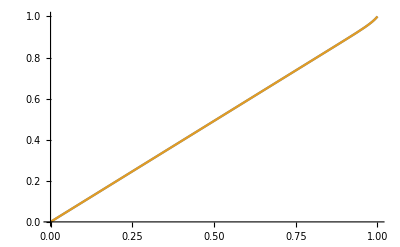

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

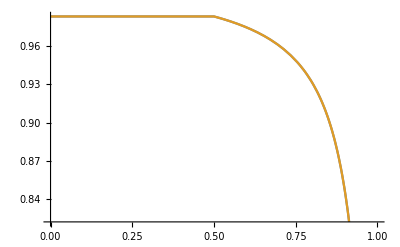

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

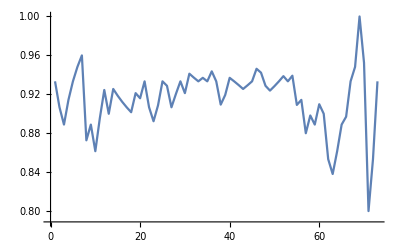

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

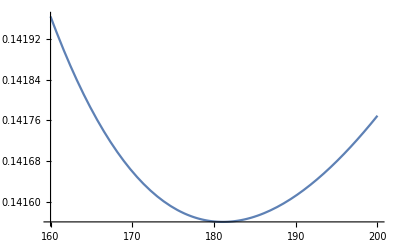

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```